# “Simple model of self-supported deformed states of isolated atoms”

### Obliczenia analityczne

1) zakładamy nieskończenie ciężkie jądro atomowe: m_n ⟶ ∞, pomijamy człon p⃗ P⃗ w równianiu (6)
2) przyjęte współrzędne na płaszczyźnie (X,Y): r⃗=(r
0), p⃗=(0
p), R⃗=(R
0), P⃗=(0
P)
3) prędkość kątowa ω w kierunku Z, więc: ω⃗ x r⃗=(0
ωr
0), ω⃗ x p⃗=(-ωp
0
0), ω⃗ x R⃗=(0
ωR
0), ω⃗ x P⃗=(-ωP
0
0)
4) równania (7) na warunki stabilności układu - przyrównujemy pochodne po czasie do zera:

Piecewise[{{p/m_e=ωr, (a)}, {P/m_c=ωR
0 = -Z/r^2+(Z-1)/(R-r)^2+ωp
0 = -kR-(Z-1)/(R-r)^2+ωP, (b)

(c)

(d)}}]

### Parametry symulacji

```mathematica
me=1; (* masa elektronu rydbergowskiego*)
mc=(Z-1); (* masa chmury elektronowej *)
k=3.5; (* stała sprężystości oscylatora *)
Z=12; (* liczba atomowa, atom magnezu Mg *)
omega=0.048; (* częstość kołowa ω obrotu *)
tmax=1500; (* maksymalny czas ewolucji układu stabilnego*)
```

### Warunki stabilności układu

```mathematica
eqs={p/me==w r, pp/mc==w rr, 0==-Z/r^2+(Z-1)/(rr-r)^2+w p, 0==-k rr - (Z-1)/(rr-r)^2+w pp} (* stabilne położenia i pędy w funkcji ω *)
```

{p==r w,pp/11==rr w,0==-12/r^2+11/(-r+rr)^2+p w,0==-3.5 rr-11/(-r+rr)^2+pp w}

```mathematica
rozw1=(rozw=NSolve[eqs/.w-> omega,{p,pp,r,rr},Reals];
rozw[[Flatten[Position[Negative[rozw[[#1,3,2]] rozw[[#1,4,2]]&@Table[i,{i,3}]],True]][[1]]]]); (* rozwiązanie układu równań dla "fizycznych" rozwiązań (rR<0) dla wybranej częstości ω *)
```

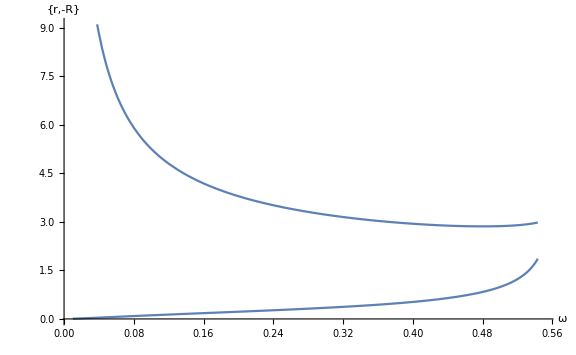

```mathematica
Plot[{r,-rr}/.(rozw=NSolve[eqs/.w-> ww,{p,pp,r,rr},Reals];rozw[[Flatten[Position[Negative[rozw[[#1,3,2]] rozw[[#1,4,2]]&@Table[i,{i,3}]],True]][[1]]]]),{ww,0.01,0.55},ImageSize->Large,AxesLabel->{"ω","{r,-R}"},BaseStyle->{Large,FontFamily->"Times",Thickness->0.003}] (* rysowanie "fizycznych" rozwiązań {r,-R} w funkcji częstości kołowej ω *)
```

### Hamiltonian

```mathematica
h=(px1^2+py1^2)/2+(pxx1^2+pyy1^2)/(2 mc)+k(xx1^2+yy1^2)/2-Z/Sqrt[x1^2+y1^2]+(Z-1)/Sqrt[(x1-xx1)^2+(y1-yy1)^2]-omega(x1 py1 - y1 px1 + xx1 pyy1 - yy1 pxx1); (* hamiltonian w układzie obracającym się z częstością ω *)
```

### Równania ruchu

```mathematica
row1={xdot1==D[h,px1],ydot1==D[h,py1],xxdot1==D[h,pxx1],yydot1==D[h,pyy1],pxdot1==-D[h,x1],pydot1==-D[h,y1],pxxdot1==-D[h,xx1],pyydot1==-D[h,yy1]}; (* równania ruchu Hamiltona *)
```

```mathematica
pod={x1->x[t],xdot1->x'[t],y1->y[t],ydot1->y'[t],xx1->xx[t],xxdot1->xx'[t],yy1->yy[t],yydot1->yy'[t],px1->px[t],pxdot1->px'[t],py1->py[t],pydot1->py'[t],pxx1->pxx[t],pxxdot1->pxx'[t],pyy1->pyy[t],pyydot1->pyy'[t]}; (* formalne podstawienia w równaniach do celu rozwiązywania ukłądu równań różniczkowych*)
```

```mathematica
row=row1/.pod; (* bezpośrednie podstawienie do równań *)
```

### Warunki początkowe

```mathematica
warpoc1={x[0]==xrown,y[0]==0,xx[0]==xxrown,yy[0]==0,px[0]==0,py[0]==pyrown,pxx[0]==0,pyy[0]==pyyrown}; (* formalne podstawienie warunków początkowych *)
```

```mathematica
warpoc=warpoc1/.{xrown->rozw1[[4,2]],xxrown->rozw1[[3,2]],pyrown->rozw1[[1,2]],pyyrown->rozw1[[2,2]]}; (* bezpośrednie podstawienie warunków początkowych *)
```

### Ewolucja układu w równowadze

```mathematica
rownania=Flatten[{row,warpoc},1]; (* lista równań i warunków początkowych *)
```

```mathematica
s=NDSolve[rownania,{x,xx,y,yy,px,pxx,py,pyy},{t,0,tmax}]; (* rozwiązanie równań ruchu w warunkach równowagi *)
```

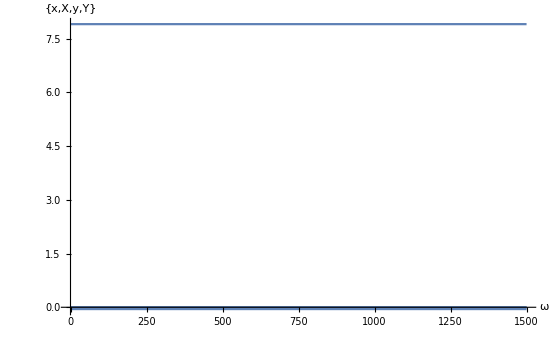

```mathematica
Plot[{x[t],xx[t],y[t],yy[t]}/.s,{t,0,tmax},AxesLabel->{"ω","{x,X,y,Y}"},BaseStyle->{Large,FontFamily->"Times",Thickness->0.003}] (* wykres dynamiki układu*)
```

### Ewolucja układu zaburzonego

```mathematica
warpoczab=warpoc1/.{xrown->rozw1[[4,2]]+0.2,xxrown->rozw1[[3,2]],pyrown->rozw1[[1,2]],pyyrown->rozw1[[2,2]]};(* bezpośrednie podstawienie zaburzonych warunków początkowych *)
```

```mathematica
rownania2=Flatten[{row,warpoczab},1];(* lista równań i warunków początkowych *)
```

```mathematica
s2=NDSolve[rownania2,{x,xx,y,yy,px,pxx,py,pyy},{t,0,tmax}];(* rozwiązanie równań ruchu dla przypadku zaburzenia *)
```

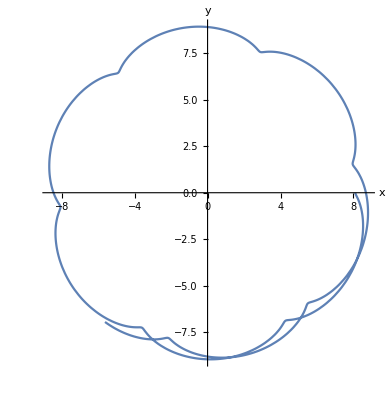

```mathematica
ParametricPlot[{x[t],y[t]}/.s2,{t,0,tmax},AxesLabel->{"x","y"},BaseStyle->{Large,FontFamily->"Times",Thickness->0.003}] (* trajektoria elektronu rydbergowskiego w układzie spoczywającym *)
```

### Przejście do układu obracającego się

```mathematica
Manipulate[ParametricPlot[{x[t] Cos[w1 t]+y[t] Sin[w1 t],-Sin[w1 t] x[t]+Cos[w1 t] y[t]}/.s2,{t,0,tmax},AxesLabel->{"x","y"},BaseStyle->{Large,FontFamily->"Times",Thickness->0.003}],{{w1,-0.0057159},-0.006,-0.005}] (* dobór odpowiedniej prędkości kątowej układu obrajacącego się*)
```

```mathematica
w1=-0.0057159; (* częstość dla przejścia do układu wirującego *)
rys1=ParametricPlot[{x[t] Cos[w1 t]+y[t] Sin[w1 t],-Sin[w1 t] x[t]+Cos[w1 t] y[t]}/.s2,{t,0,tmax},AxesLabel->{"x","y"},BaseStyle->{Large,FontFamily->"Times",Thickness->0.003}];(* trajektoria ruchu zaburzonego elektronu rydbergowskiego *)
rys2=ParametricPlot[{xx[t] Cos[w1 t]+yy[t] Sin[w1 t],-Sin[w1 t] xx[t]+Cos[w1 t] yy[t]}/.s2,{t,0,tmax},AxesLabel->{"X","Y"},BaseStyle->{Large,FontFamily->"Times",Thickness->0.003}]; (* trajektoria ruchu zaburzonego rdzenia *)
```

### Trajektorie ruchu elektronu walencyjnego i rdzenia

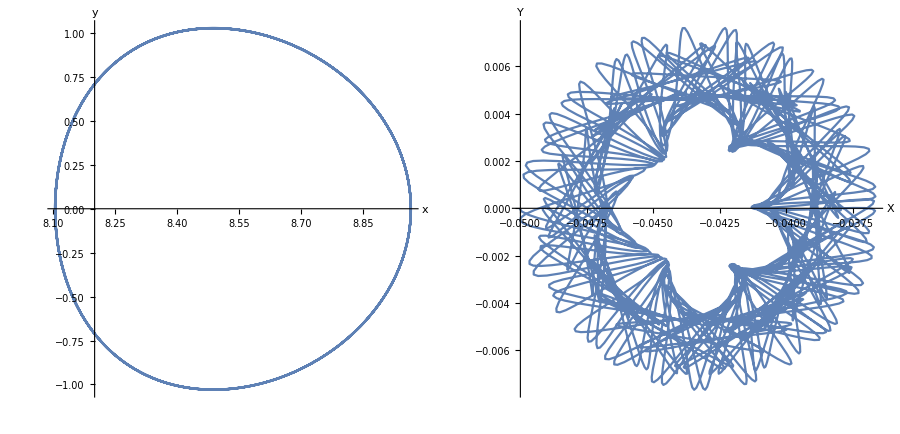

```mathematica
GraphicsGrid[{{rys1,rys2}},ImageSize->900]
```